```mathematica
data={
{10,0.0254,0.0062,40,0,2.77556*10^-16,5.55112*10^-17},{100,2.4661,0.0677,40,0,1.11577*10^-14,2.49800*10^-16},{500,56.5298,0.1839,68,24,5.33462*10^-14,1.33227*10^-15},
{1000,214.188,0.6459,96,12,1.14325*10^-13,3.99680*10^-15},{
2000,873.031,1.4639,164,96,2.28373*10^-13,2.83107*10^-15},
{5000,5388.74,5.1823,280,384,5.27550*10^-13,1.13798*10^-14},
{10000,21692.8,9.4022,512,772,1.24636*10^-12,7.49401*10^-14},
{20000,62857.1,12.402,936,1548,2.87743*10^-12,2.03670*10^-13}};

(*Распакуем столбцы*)
Nvals=data[[All,1]];
DFTtime=data[[All,2]];
FFTtime=data[[All,3]];
DFTmem=data[[All,4]];
FFTmem=data[[All,5]];
DFTerr=data[[All,6]];
FFTerr=data[[All,7]];
```

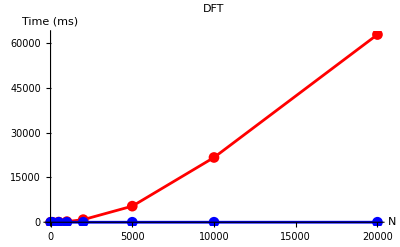

```mathematica
Show[ListLinePlot[Transpose[{Nvals,DFTtime}],PlotStyle->Red,Joined->True,PlotMarkers->Automatic,AxesLabel->{"N","Time (ms)"},PlotLabel->"DFT"],ListLinePlot[Transpose[{Nvals,FFTtime}],PlotStyle->Blue,Joined->True,PlotMarkers->Automatic,AxesLabel->{"N","Time (ms)"},PlotLabel->"FFT"]]
```

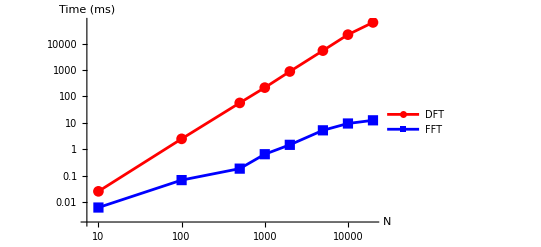

```mathematica
ListLogLogPlot[{Transpose[{Nvals,DFTtime}],Transpose[{Nvals,FFTtime}]},PlotStyle->{Red,Blue},Joined->True,PlotMarkers->Automatic,AxesLabel->{"N","Time (ms)"},PlotLegends->{"DFT","FFT"},GridLines->Automatic]
```

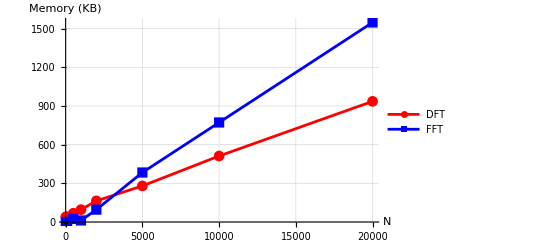

```mathematica
ListLinePlot[{Transpose[{Nvals,DFTmem}],Transpose[{Nvals,FFTmem}]},PlotStyle->{Red,Blue},PlotMarkers->Automatic,AxesLabel->{"N","Memory (KB)"},PlotLegends->{"DFT","FFT"},GridLines->Automatic]
```

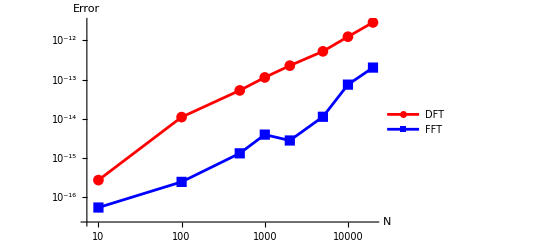

```mathematica
ListLogLogPlot[{Transpose[{Nvals,DFTerr}],Transpose[{Nvals,FFTerr}]},PlotStyle->{Red,Blue},Joined->True,PlotMarkers->Automatic,AxesLabel->{"N","Error"},PlotLegends->{"DFT","FFT"},GridLines->Automatic]
```